```mathematica
Directory[]
```

C:\Users\Rebeca Alvarado\Documents

```mathematica
tot=11;
```

```mathematica
TSC=Import["C:\\Users\\Rebeca Alvarado\\Documents\\Licenciatura\\8Semestre\\Computo de alto rendimiento\\P1\\P1-Hash_tables\\tiempos_SC.txt", "Table"];
TOAL=Import["C:\\Users\\Rebeca Alvarado\\Documents\\Licenciatura\\8Semestre\\Computo de alto rendimiento\\P1\\P1-Hash_tables\\tiempos_OA-lineal.txt", "Table"];
TOAQ=Import["C:\\Users\\Rebeca Alvarado\\Documents\\Licenciatura\\8Semestre\\Computo de alto rendimiento\\P1\\P1-Hash_tables\\tiempos_OA-quad.txt", "Table"];
TOADH1=Import["C:\\Users\\Rebeca Alvarado\\Documents\\Licenciatura\\8Semestre\\Computo de alto rendimiento\\P1\\P1-Hash_tables\\tiempos_OA-double1.txt", "Table"];
```

```mathematica
ListLinePlot
```

```mathematica
t2=Table[{TOAL[[i,1]], TOAL[[i,2]]},{i, 1, 11}]
```

{{1000,0.0032},{5000,0.0228},{10000,0.0514},{50000,0.2044},{100000,0.3448},{500000,1.3994},{1000000,2.6923},{2500000,6.8275},{3200000,7.30375},{4000000,9.4785},{5000000,11.256}}

```mathematica
TOAL[[1;;11,1;;2]]
```

{{1000,0.0032},{5000,0.0228},{10000,0.0514},{50000,0.2044},{100000,0.3448},{500000,1.3994},{1000000,2.6923},{2500000,6.8275},{3200000,7.30375},{4000000,9.4785},{5000000,11.256}}

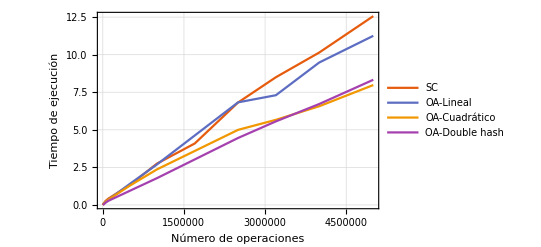

```mathematica
G1=ListLinePlot[{TSC⟦1;;12,1;;2⟧,TOAL⟦1;;tot,1;;2⟧, TOAQ⟦1;;tot,1;;2⟧, TOADH1⟦1;;tot,1;;2⟧}, PlotLegends->Placed[{"SC", "OA-Lineal", "OA-Cuadrático", "OA-Double hash"},Above], PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Número de operaciones", "Tiempo de ejecución (s)"}]
```

```mathematica
Export["Graficas1.pdf",G1]
```

Graficas1.pdf

```mathematica
OAL9={{10000, 0.193330},{50000,0.193750},{100000, 0.446800}, {500000,1.770667},{1000000,3.437667}, {2500000, 9.283000},{3700000,14.75400},{5000000,20.57900}};
OAD9={{10000, 0.02},{50000,0.11},{100000, 0.192},{250000, 1.213},{400000, 5.829},{450000, 13.857}, {500000,23.88315},{1000000,179.622}};
SC9={{10000, 0.028},{50000,0.14467},{100000, 0.240000}, {500000,1.216667},{1000000,2.4003}, {2500000,4.149},{4000000,9.201},{5000000,12.27333}};

OAQ9={{10000, 0.0206},{50000,0.1487},{100000, 0.31225}, {500000,4.20725},{600000,12.4613}, {700000, 31.135},{800000,51.8275},{900000,90.79}, {1000000,107.310}};
```

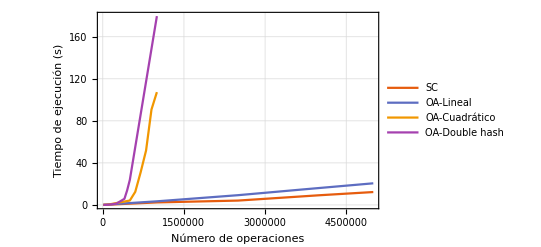

Graficas90.pdf

```mathematica
G2=ListLinePlot[{SC9,OAL9, OAQ9, OAD9}, PlotLegends->Placed[{"SC", "OA-Lineal", "OA-Cuadrático", "OA-Double hash"},Above], PlotTheme->"Scientific", GridLines->Automatic, PlotRange->Full,FrameLabel->{"Número de operaciones", "Tiempo de ejecución (s)"}]
Export["Graficas90.pdf",G2]
```

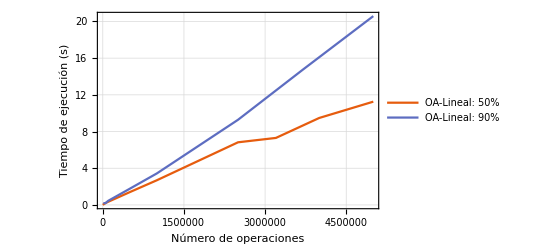

```mathematica
GOAL=ListLinePlot[{TOAL⟦1;;tot,1;;2⟧, OAL9}, PlotLegends->Placed[{ "OA-Lineal: 50%", "OA-Lineal: 90%"},Above], PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Número de operaciones", "Tiempo de ejecución (s)"}]
```

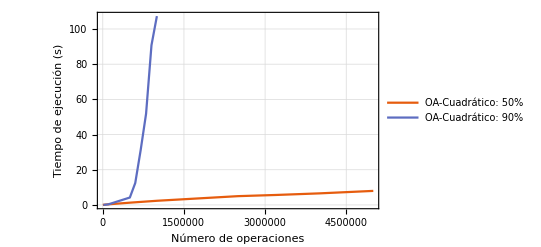

```mathematica
GOAQ=ListLinePlot[{TOAQ⟦1;;tot,1;;2⟧, OAQ9}, PlotLegends->Placed[{ "OA-Cuadrático: 50%", "OA-Cuadrático: 90%"},Above], PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Número de operaciones", "Tiempo de ejecución (s)"}]
```

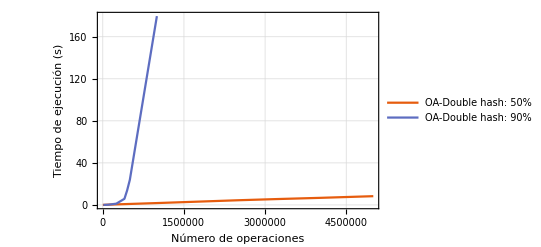

```mathematica
GOAD=ListLinePlot[{TOADH1⟦1;;tot,1;;2⟧, OAD9}, PlotLegends->Placed[{ "OA-Double hash: 50%", "OA-Double hash: 90%"},Above], PlotRange->Full, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Número de operaciones", "Tiempo de ejecución (s)"}]
```

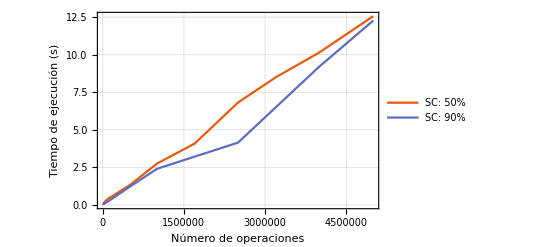

```mathematica
GSC=ListLinePlot[{TSC⟦1;;12,1;;2⟧, SC9}, PlotLegends->Placed[{ "SC: 50%", "SC: 90%"},Above], PlotRange->Full, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Número de operaciones", "Tiempo de ejecución (s)"}]
```

```mathematica
Export["GraficasOAL.pdf",GOAL]
Export["GraficasOAD.pdf",GOAD]
Export["GraficasOAQ.pdf",GOAQ]
Export["GraficasSC.pdf",GSC]
```

GraficasOAL.pdf

GraficasOAD.pdf

GraficasOAQ.pdf

GraficasSC.pdf